```mathematica
blue=RGBColor[{91,194,231}/255] (* Zima Blue *)
orange=RGBColor[{231,128,91}/255] (* Complementary Zima Blue *)
lighting={DirectionalLight[RGBColor[0.5{1,1,1}],{{1,1,1},{0,0,0}}],{"Ambient",RGBColor[0.8{1,1,1}]}}
```

RGBColor[{Rational[91, 255], Rational[194, 255], Rational[77, 85]}]

RGBColor[{Rational[77, 85], Rational[128, 255], Rational[91, 255]}]

{DirectionalLight[RGBColor[{0.5, 0.5, 0.5}],{{1,1,1},{0,0,0}}],{Ambient,RGBColor[{0.8, 0.8, 0.8}]}}

```mathematica
Graphics3D[{blue,Octahedron[]},Lighting->lighting]
```

-Graphics3D-

```mathematica
(* Replace Abs with MyAbs to have Det of Jacobian differentiable *)
```

```mathematica
MyAbs[x_]:=√(x^2)
MyAbs[x_List]:=MyAbs/@x
MyMin[x_,y_]:=(x+y-Abs[x-y])/2 (* No used *)
MyMax[x_,y_]:=(x+y+Abs[x-y])/2 (* No used *)
MyNormalize[x_]:=x/(√(x.x))
Lerp[a_,b_,t_]:=a*(1-t)+b*t
Lerp[a_List,b_List,t_]:=Map[Lerp[#⟦1⟧,#⟦2⟧,t]&,{a,b}ᵀ,{1}]
Clamp[x_,bound_]:=MyMax[MyMin[x,bound⟦2⟧],bound⟦1⟧]
Clamp[x_List,bound_]:=Clamp[#,bound]&/@x
```

```mathematica
(* Default Implementation *)
```

```mathematica
PackNormalOctQuadEncode[n_]:=Module[{md,rcp,tn,t,ts},
If[#>=0,
#+Clip[-(n/Max[Dot[Abs[n],{1,1,1}],10^-6])⟦3⟧,{0,1}],
#-Clip[-(n/Max[Dot[Abs[n],{1,1,1}],10^-6])⟦3⟧,{0,1}]]&/@(n/Max[Dot[Abs[n],{1,1,1}],10^-6])⟦;;2⟧
]
```

```mathematica
UnpackNormalOctQuadEncode[f_]:=Module[{n,t,ts,nxy},
ts=Flatten[{
If[#>=0,
#-Max[-(1-Abs[f⟦1⟧]Abs[f⟦2⟧]),0],
#+Max[-(1-Abs[f⟦1⟧]-Abs[f⟦2⟧]),0]]&/@{f⟦1⟧,f⟦2⟧},
1-Abs[f⟦1⟧]-Abs[f⟦2⟧]
}];
Normalize[ts]
]
```

```mathematica
(* Without Clamping, for Shader/GPU implementation please be aware of numerical instabilities (Division by near zero or zero), but mathematically for derivation we don't consider them. *)
PackNormalOctQuadEncode[n_]:=Module[{md,rcp,tn,t,ts},
If[#>=0,
#+Clip[-(n/Dot[Abs[n],{1,1,1}])⟦3⟧,{0,1}],
#-Clip[-(n/Dot[Abs[n],{1,1,1}])⟦3⟧,{0,1}]]&/@(n/Dot[Abs[n],{1,1,1}])⟦;;2⟧
]
```

```mathematica
(* Default Implementation with singularities *)
```

```mathematica
PackNormalOctQuadEncode[n_]:=Module[{md,rcp,tn,t,ts},
If[#>=0,
#+Clip[-(n/Dot[Abs[n],{1,1,1}])⟦3⟧,{0,1}],
#-Clip[-(n/Dot[Abs[n],{1,1,1}])⟦3⟧,{0,1}]]&/@(n/Dot[Abs[n],{1,1,1}])⟦;;2⟧
]
```

```mathematica
UnpackNormalOctQuadEncode[f_]:=Module[{n,t,ts,nxy},
ts=Flatten[{
If[#>=0,
#-Max[-(1-Abs[f⟦1⟧]Abs[f⟦2⟧]),0],
#+Max[-(1-Abs[f⟦1⟧]-Abs[f⟦2⟧]),0]]&/@{f⟦1⟧,f⟦2⟧},
1-Abs[f⟦1⟧]-Abs[f⟦2⟧]
}];
Normalize[ts]
]
```

```mathematica
(* Differentiable Implementation *)
```

```mathematica
PackNormalOctQuadEncode[n_]:=Module[{md,rcp,tn,t,ts},
If[#>=0,
#+Clamp[-(n/Dot[MyAbs[n],{1,1,1}])⟦3⟧,{0,1}],
#-Clamp[-(n/Dot[MyAbs[n],{1,1,1}])⟦3⟧,{0,1}]
]&/@(n/Dot[MyAbs[n],{1,1,1}])⟦;;2⟧
]
```

```mathematica
UnpackNormalOctQuadEncode[f_]:=Module[{n,t,ts,nxy},
ts=Flatten[{
If[#>=0,
#-Max[-(1-MyAbs[f⟦1⟧]-MyAbs[f⟦2⟧]),0],
#+Max[-(1-MyAbs[f⟦1⟧]-MyAbs[f⟦2⟧]),0]]&/@{f⟦1⟧,f⟦2⟧},
1-MyAbs[f⟦1⟧]-MyAbs[f⟦2⟧]
}];
MyNormalize[ts]
]
```

```mathematica
(* Full Jacobian *)
```

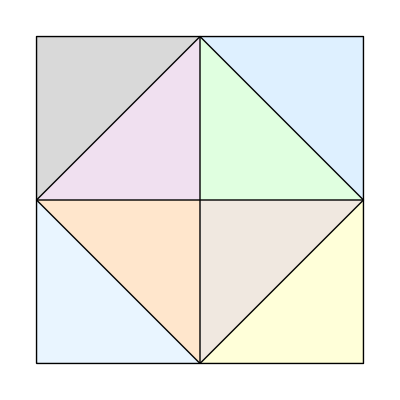

```mathematica
Graphics[{
{LightGreen,Triangle[{{0,0},{1,0},{0,1}}]},
{LightPurple,Triangle[{{0,0},{0,1},{-1,0}}]},
{LightOrange,Triangle[{{0,0},{-1,0},{0,-1}}]},
{LightBrown,Triangle[{{0,0},{0,-1},{1,0}}]},
{LightBlue,Triangle[{{1,0},{1,1},{0,1}}]},
{LightGray,Triangle[{{0,1},{-1,1},{-1,0}}]},
{Lighter[LightBlue],Triangle[{{-1,0},{-1,-1},{0,-1}}]},
{LightYellow,Triangle[{{0,-1},{1,-1},{1,0}}]},
Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}],
Line[{{0,-1},{-1,0},{0,1},{1,0},{0,-1}}],
Line[{{0,-1},{0,1}}],
Line[{{-1,0},{1,0}}]
}]
```

```mathematica
(* Full Jacobian from non-differentiable version *)
```

```mathematica
(Abs[1-Abs[u]-Abs[v]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] (If[v≥0,1-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}])] Abs'[u]-If[v≥0,-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}]] Abs'[v]) Abs'[1-Abs[u]-Abs[v]]-If[u≥0,-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}]] (Abs[1-Abs[u]-Abs[v]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[u] Abs'[1-Abs[u]-Abs[v]]+If[v≥0,-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}]] (1+u^2+v^2+2 Abs[u] (-1+Abs[v])-2 Abs[v]+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2-Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]-Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]))+If[u≥0,1-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}])] (Abs[1-Abs[u]-Abs[v]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[v] Abs'[1-Abs[u]-Abs[v]]+If[v≥0,1-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}])] (1+u^2+v^2+2 Abs[u] (-1+Abs[v])-2 Abs[v]+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2-Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]-Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]])))/((-1+Abs[u]+Abs[v])^2+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2)^2
```

(Abs[1-Abs[u]-Abs[v]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] (If[v≥0,1-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}])] Abs'[u]-If[v≥0,-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}]] Abs'[v]) Abs'[1-Abs[u]-Abs[v]]-If[u≥0,-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}]] (Abs[1-Abs[u]-Abs[v]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[u] Abs'[1-Abs[u]-Abs[v]]+If[v≥0,-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}]] (1+u^2+v^2+2 Abs[u] (-1+Abs[v])-2 Abs[v]+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2-Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]-Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]))+If[u≥0,1-(Piecewise[{{Abs[v] Abs'[u], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[u], Abs[u]+Abs[v]>1}, {0, True}}])] (Abs[1-Abs[u]-Abs[v]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[v] Abs'[1-Abs[u]-Abs[v]]+If[v≥0,1-(Piecewise[{{Abs[u] Abs'[v], Abs[u] Abs[v]>1}, {0, True}}]),1+(Piecewise[{{Abs'[v], Abs[u]+Abs[v]>1}, {0, True}}])] (1+u^2+v^2+2 Abs[u] (-1+Abs[v])-2 Abs[v]+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2-Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]-Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]] If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]] Abs'[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]])))/((-1+Abs[u]+Abs[v])^2+Abs[If[u≥0,u-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],u+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2+Abs[If[v≥0,v-Max[-(1-Abs[{u,v}⟦1⟧] Abs[{u,v}⟦2⟧]),0],v+Max[-(1-Abs[{u,v}⟦1⟧]-Abs[{u,v}⟦2⟧]),0]]]^2)^2

```mathematica
(* Full Jacobian from non-differentiable version *)
```

```mathematica
FullSimplify[Det[Append[D[UnpackNormalOctQuadEncode[{u,v}],{{u,v}}]ᵀ,{0,0,1}]ᵀ],Assumptions->-1<=u<=1&&-1<=v<=1]
```

Piecewise[{{(1+u-v)/((1-2 v+2 (u+u^2-u v+v^2))^2), u<0&&v>0&&1+u≥v}, {((-1+u) (1+2 u))/(1+2 u (1+u))^2, u<0&&v==0}, {-(1+v)/(1+2 v (1+v))^2, u==0&&v<0}, {(1-u+v)/((1+2 u^2-2 u (1+v)+2 v (1+v))^2), u>0&&v<0&&u≤1+v}, {-(-1+u+v)/((1+2 u^2+2 u (-1+v)+2 (-1+v) v)^2), u≥0&&v≥0&&u+v≤1}, {(1+u+v)/((1+2 v+2 (u+u^2+u v+v^2))^2), u<0&&v<0&&1+u+v≥0}, {(1+u-v)/((3+2 u^2-2 u (-2+v)+2 (-2+v) v)^2), 1+u<v}, {-(-1+u+v)/((3+2 u^2+2 u (-2+v)+2 (-2+v) v)^2), u+v>1}, {(1-u+v)/((3+2 u^2-2 u (2+v)+2 v (2+v))^2), u>1+v}, {(1+u+v)/((3+2 u^2+2 u (2+v)+2 v (2+v))^2), True}}]

```mathematica
(* Green Zone Jacobian *)
```

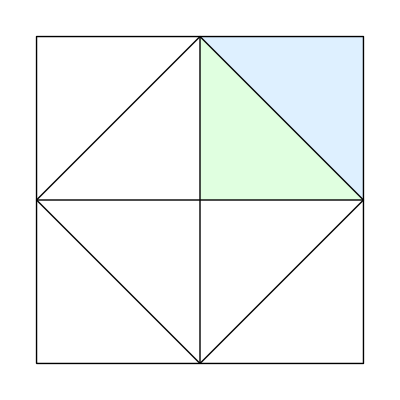

```mathematica
Graphics[{
{LightGreen,Triangle[{{0,0},{1,0},{0,1}}]},
{LightBlue,Triangle[{{1,0},{1,1},{0,1}}]},
Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}],
Line[{{0,-1},{-1,0},{0,1},{1,0},{0,-1}}],
Line[{{0,-1},{0,1}}],
Line[{{-1,0},{1,0}}]
}]
```

```mathematica
Clear[{JacBlue,JacGreen}]
(* Blue Zone *)
JacBlue[u_,v_]=FullSimplify[MyAbs@Det[Append[D[UnpackNormalOctQuadEncode[{u,v}],{{u,v}}]ᵀ,{0,0,1}]ᵀ],Assumptions->0<=u<=1&&0<=v<=1&&u+v>1]
(* Green Zone *)
JacGreen[u_,v_]=FullSimplify[MyAbs@Det[Append[D[UnpackNormalOctQuadEncode[{u,v}],{{u,v}}]ᵀ,{0,0,1}]ᵀ],Assumptions->0<=u<=1&&0<=v<=1&&u+v<1]
```

(-1+u+v)/((3+2 u^2+2 u (-2+v)+2 (-2+v) v)^2)

-(-1+u+v)/((1+2 u^2+2 u (-1+v)+2 (-1+v) v)^2)

```mathematica
Plot3D[{
If[u+v>1,JacBlue[u,v],Nothing],
If[u+v<1,JacGreen[u,v],Nothing]},
{u,0,1},{v,0,1},PlotStyle->{blue,LightGreen},PlotRange->All,Boxed->False,Lighting->lighting]
```

-Graphics3D-

```mathematica
(* Change of variable *)
```

```mathematica
(* Some Observations *)
```

```mathematica
Plot3D[{JacBlue[u,v],JacBlue[1-u,1-v]},{u,0,1},{v,0,1},PlotStyle->{blue,orange},PlotRange->All,Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[{
JacGreen[Abs[u],Abs[v]],
JacBlue[Abs[u],Abs[v]]
},{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->{LightGreen,blue},Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[Max[JacGreen[Abs[u],Abs[v]],JacBlue[Abs[u],Abs[v]]],{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->blue,Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[
Evaluate@Module[{s,ss,uu,vv},
s=Sign[Abs[u]+Abs[v]-1];
ss=s/2+1/2;
uu=Lerp[Abs[u],1-Abs[u],ss];
vv=Lerp[Abs[v],1-Abs[v],ss];
{s*JacGreen[uu,vv],JacGreen[Abs[u],Abs[v]],JacBlue[Abs[u],Abs[v]]}
],{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->{blue,orange,LightGreen},Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[
Evaluate@Module[{s,ss,uu,vv},
s=Sign[Abs[u]+Abs[v]-1];
ss=s/2+1/2;
uu=Lerp[Abs[u],1-Abs[u],ss];
vv=Lerp[Abs[v],1-Abs[v],ss];
-s*JacGreen[uu,vv]
],{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->blue,Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[1/2((1-2Abs[u])Sign[Abs[u]+Abs[v]-1]+1),
{u,-1,1},{v,-1,1},Axes->{True,True,True},AxesLabel->{Style["u",Bold,FontSize->32],Style["v",Bold,FontSize->32],Style["ũ",Bold,FontSize->32]},PlotStyle->orange,Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[1/2((1-2Abs[v])Sign[Abs[u]+Abs[v]-1]+1),
{u,-1,1},{v,-1,1},Axes->{True,True,True},AxesLabel->{Style["u",Bold,FontSize->32],Style["v",Bold,FontSize->32],Style["OverTilde[v\n]",Bold,FontSize->32]},PlotStyle->blue,Lighting->lighting]
```

-Graphics3D-

```mathematica
Plot3D[{
1/2((1-2Abs[u])Sign[Abs[u]+Abs[v]-1]+1),
1/2((1-2Abs[v])Sign[Abs[u]+Abs[v]-1]+1)
},
{u,-1,1},{v,-1,1},PlotStyle->{{blue,Opacity[0.5]},{orange,Opacity[0.5]}},Boxed->False,Lighting->lighting]
```

-Graphics3D-

```mathematica
(* Full Jacobian *)
```

```mathematica
FullJac[u_,v_]:=Module[{s,ss,uu,vv},
s=Sign[Abs[u]+Abs[v]-1];
ss=s/2+1/2;
uu=Lerp[Abs[u],1-Abs[u],ss];
vv=Lerp[Abs[v],1-Abs[v],ss];
JacGreen[uu,vv]
]
```

```mathematica
(* Heavy Expression *)
```

```mathematica
FullJac[u,v]
```

-((-1+Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))/(1+2 (Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))^2+2 (Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])) (-1+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))+2 (-1+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])) (Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])))^2)

```mathematica
Plot3D[FullJac[u,v],{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->blue,Lighting->lighting]
```

-Graphics3D-

```mathematica
(* Mathematica do your thing! *)
```

```mathematica
OctJac[u_,v_]=FullSimplify[FullJac[u,v],Assumptions->{Element[_,Reals]&&-1<u<1&&-1<v<1}]
```

Abs[-1+Abs[u]+Abs[v]]/((-2 (1+u^2+v^2)+Abs[u] (3-2 Abs[v])+3 Abs[v]+Abs[-1+Abs[u]+Abs[v]])^2)

```mathematica
Plot3D[OctJac[u,v],{u,-1,1},{v,-1,1},PlotRange->All,PlotStyle->orange,Lighting->lighting]
```

-Graphics3D-

```mathematica
(* Proposed Simple Scalar Implementation *)
```

```mathematica
Experimental`OptimizeExpression[OctJac[u,v],OptimizationLevel->2,OptimizationSymbol->j]
```

Experimental`OptimizedExpression[Block[{j11,j12,j13,j14,j7,j8,j15,j16,j17,j18,j9,j10,j19,j20,j21},j11=u^2;j12=v^2;j13=1+j11+j12;j14=-2 j13;j7=Abs[u];j8=Abs[v];j15=-2 j8;j16=3+j15;j17=j7 j16;j18=3 j8;j9=-1+j7+j8;j10=Abs[j9];j19=j14+j17+j18+j10;j20=j19^2;j21=1/j20;j10 j21]]

```mathematica
CSEJac[u_,v_]:=Module[{j11,j12,j13,j14,j7,j8,j15,j16,j17,j18,j9,j10,j19,j20,j21},j11=u^2;
j12=v^2;j13=1+j11+j12;j14=-2 j13;j7=Abs[u];j8=Abs[v];j15=-2 j8;j16=3+j15;j17=j7 j16;j18=3 j8;j9=-1+j7+j8;j10=Abs[j9];j19=j14+j17+j18+j10;j20=j19^2;j21=1/j20;j10 j21]
```

```mathematica
CSEJac[u,v]
OctJac[u,v]
FullJac[u,v]
```

Abs[-1+Abs[u]+Abs[v]]/((-2 (1+u^2+v^2)+Abs[u] (3-2 Abs[v])+3 Abs[v]+Abs[-1+Abs[u]+Abs[v]])^2)

Abs[-1+Abs[u]+Abs[v]]/((-2 (1+u^2+v^2)+Abs[u] (3-2 Abs[v])+3 Abs[v]+Abs[-1+Abs[u]+Abs[v]])^2)

-((-1+Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))/(1+2 (Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))^2+2 (Abs[u] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[u]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])) (-1+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]]))+2 (-1+Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])) (Abs[v] (1/2-1/2 Sign[-1+Abs[u]+Abs[v]])+(1-Abs[v]) (1/2+1/2 Sign[-1+Abs[u]+Abs[v]])))^2)

```mathematica
OpCount[CSEJac[u,v]]
OpCount[OctJac[u,v]]
OpCount[FullJac[u,v]]
```

16

16

27

```mathematica
CForm[OctJac[u,v]]/.{Power->pow,Abs->abs}
```

abs(-1 + abs(u) + abs(v))*pow(abs(u)*(3 - 2*abs(v)) + 3*abs(v) + abs(-1 + abs(u) + abs(v)) - 2*(1 + pow(u,2) + pow(v,2)),-2)